```mathematica
(* Calculate the effective nonlinearities for 3d lattices (periodic boundary conditions)
```

```mathematica
(* Absorbing state (in vitro) networks: nonlinearity defined for x ≥ 0
```

```mathematica
(* The eigenvalue distribution is calculated for each value of J, so be sure not to mix up evaluation of cells for different values of J.
```

```mathematica
(* Eigenvalue threshold, parametrized in terms of k \in [0,1]
```

```mathematica
Λk[k_,Λmax_,Λmin_] := ((Λmax-Λmin)*k+Λmin)
```

```mathematica
(* =================================================================================== *)
```

```mathematica
(* Calculate eigenvalue density
```

```mathematica
(* =================================================================================== *)
```

```mathematica
(* Extract spectrum (A = -Im(G)/Pi)
```

```mathematica
d = 3;
```

```mathematica
A3[x_?NumericQ] := -0.125*NIntegrate[Piecewise[{{0,x ≤ -3},{(2*BesselK[0,t]/Pi)*(2*(2*BesselK[0,t]/Pi)^2*Cosh[x*t]-3*(2*BesselI[0,t])^2*Exp[x*t]),-3 < x ≤ -1},{-4*(2*BesselK[0,t]/Pi)^3*Cosh[x*t],-1 < x ≤ 1},{(2*BesselK[0,t]/Pi)*(2*(2*BesselK[0,t]/Pi)^2*Cosh[x*t]-3*(2*BesselI[0,t])^2*Exp[-x*t]),1 < x ≤ 3},{0,3 ≤ x}}],{t,0,Infinity}]/Pi
```

```mathematica
(* This definition will take too long if we run it in NDSolve, so for each choice of J0 we will first create a table of sampled points and define an interpolation function.
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 0.4125 (Jc/2)
```

```mathematica
(* =================== *)
```

```mathematica
J0 =0.4125;
```

```mathematica
Λmax = J0*(2*d-1);
```

```mathematica
Λmin = -J0*(2*d+1);
```

```mathematica
A3lamtbl = Table[{x,A3[(x/J0+1)/2]/2/J0},{x,Λmin,Λmax,0.001}];
```

```mathematica
Export["Latticedensity_d3_J0p4125.txt",A3lamtbl,"Table"];
```

```mathematica
A3fun = Interpolation[A3lamtbl]
```

InterpolatingFunction[…]

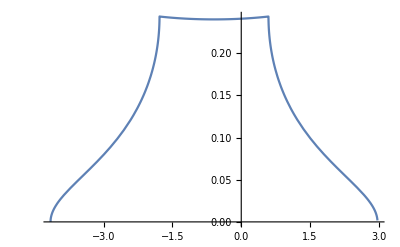

```mathematica
Plot[A3fun[x],{x,Λmin,Λmax},PlotRange->All]
```

```mathematica
(* Check that distribution integrates to (close to) 1
```

```mathematica
NIntegrate[A3fun[x],{x,Λmin,Λmax}]
```

0.999993

```mathematica
(* Function to solve system of equations for effective nonlinearities
```

```mathematica
PhisolnO4lattice[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{500}}}}]
```

```mathematica
PhiO4lattd3J0p4125 = PhisolnO4lattice[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[…],Φ2→InterpolatingFunction[…],Φ3→InterpolatingFunction[…],Φ4→InterpolatingFunction[…]}}

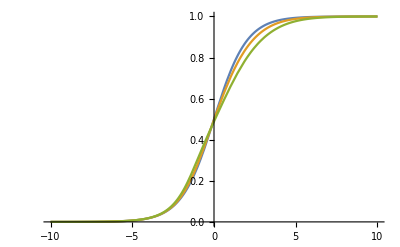

```mathematica
Plot[{LogisticSigmoid[y],Evaluate[Φ1[1,y]/.PhiO4lattd3J0p4125],Evaluate[Φ2[1,y]/.PhiO4lattd3J0p4125]},{y,-10,10}]
```

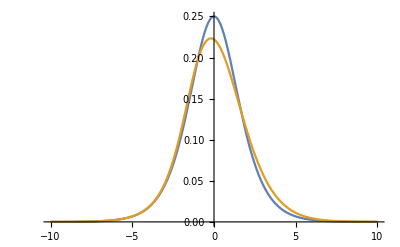

```mathematica
Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J0p4125},{y,-10,10}]
```

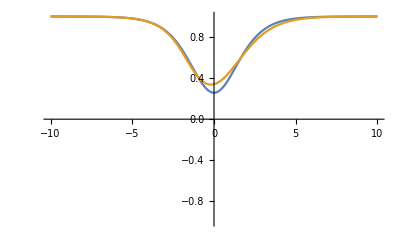

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J0p4125},{y,-10,10},PlotRange->{-1,1}]
```

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J0p4125},{y,-10,10}],{k,0,1}]
```

```mathematica
FindRoot[{Derivative[0,2][Φ1][1,y]==0/.PhiO4lattd3J0p4125},{y,0}]
```

{y→-0.187937}

```mathematica
Φ1[1,-0.18793657021458793]/.PhiO4lattd3J0p4125
```

{0.455381}

```mathematica
1-Λmax*Derivative[0,1][Φ1][1,-0.18793657021458793]/.PhiO4lattd3J0p4125
```

{0.33676}

```mathematica
thetatbld3J0p4125 = Table[{Λk[k,Λmax,Λmin],y/.FindRoot[{Derivative[0,2][Φ1][k,y]==0/.PhiO4lattd3J0p4125},{y,0}]},{k,0,1,0.01}];
```

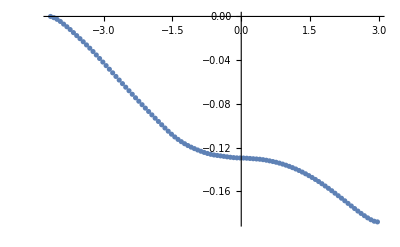

```mathematica
ListPlot[thetatbld3J0p4125]
```

```mathematica
masstblJ0p4125 = Table[{Λk[k,Λmax,Λmin],1-Λk[k,Λmax,Λmin]*Derivative[0,1][Φ1][k,y/.FindRoot[Derivative[0,2][Φ1][k,y]==0/.PhiO4lattd3J0p4125,{y,0}]]/.PhiO4lattd3J0p4125//Last},{k,0,1,0.01}];
```

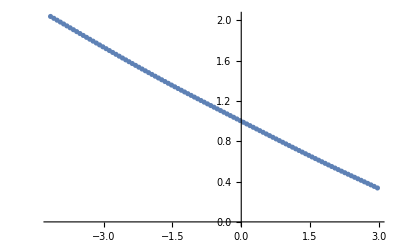

```mathematica
ListPlot[masstblJ0p4125]
```

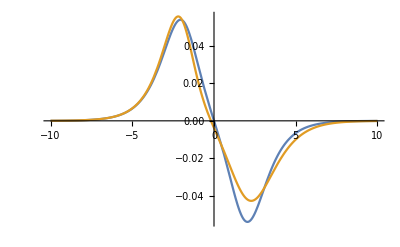

```mathematica
Plot[{LogisticSigmoid''[y]/(1+(1.05*(2*d-1)*LogisticSigmoid'[y])^2)^(3/2),Derivative[0,2][Φ1][1,y]/(1+(1.05*(2*d-1)*Derivative[0,1][Φ1][1,y])^2)^(3/2)/.PhiO4lattd3J0p4125},{y,-10,10}]
```

```mathematica
PhiO4lattJ0p4125tbl = Table[{y,Last[Evaluate[Φ1[1,y]/.PhiO4lattd3J0p4125]],Last[Evaluate[Φ2[1,y]/.PhiO4lattd3J0p4125]],Last[Evaluate[Φ3[1,y]/.PhiO4lattd3J0p4125]]},{y,-10,10,0.05}];
```

```mathematica
Export["NPRGPhi_lattice_d3_absorbingsigmoid_J0p4125_O4.txt",PhiO4lattJ0p4125tbl,"Table"];
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 0.825 (Jc)
```

```mathematica
(* =================== *)
```

```mathematica
J0 =0.825;
```

```mathematica
Λmax = J0*(2*d-1);
```

```mathematica
Λmin = -J0*(2*d+1);
```

```mathematica
A3lamtbl = Table[{x,A3[(x/J0+1)/2]/2/J0},{x,Λmin,Λmax,0.001}];
```

```mathematica
Export["Latticedensity_d3_J0p825.txt",A3lamtbl,"Table"];
```

```mathematica
A3fun = Interpolation[A3lamtbl]
```

InterpolatingFunction[…]

```mathematica
Plot[A3fun[x],{x,Λmin,Λmax},PlotRange->All]
```

-Graphics-

```mathematica
(* Check that distribution integrates to (close to) 1
```

```mathematica
NIntegrate[A3fun[x],{x,Λmin,Λmax}]
```

0.999993

```mathematica
(* Function to solve system of equations for effective nonlinearities
```

```mathematica
PhisolnO4lattice[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{500}}}}]
```

```mathematica
PhiO4lattd3J0p825 = PhisolnO4lattice[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[…],Φ2→InterpolatingFunction[…],Φ3→InterpolatingFunction[…],Φ4→InterpolatingFunction[…]}}

```mathematica
Plot[{LogisticSigmoid[y],Evaluate[Φ1[1,y]/.PhiO4lattd3J0p825],Evaluate[Φ2[1,y]/.PhiO4lattd3J0p825]},{y,-10,10}]
```

-Graphics-

```mathematica
Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J0p825},{y,-10,10}]
```

-Graphics-

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J0p825},{y,-10,10},PlotRange->{-1,1}]
```

-Graphics-

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J0p825},{y,-10,10}],{k,0,1}]
```

ReplaceAll::reps: {PhiO4lattd3J0p594} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
FindRoot[{Derivative[0,2][Φ1][1,y]==0/.PhiO4lattd3J0p825},{y,0}]
```

{y→-0.187937}

```mathematica
Φ1[1,-0.18793657021458793]/.PhiO4lattd3J0p825
```

{0.455381}

```mathematica
1-Λmax*Derivative[0,1][Φ1][1,-0.18793657021458793]/.PhiO4lattd3J0p825
```

{0.33676}

```mathematica
thetatbld3J0p825 = Table[{Λk[k,Λmax,Λmin],y/.FindRoot[{Derivative[0,2][Φ1][k,y]==0/.PhiO4lattd3J0p825},{y,0}]},{k,0,1,0.01}];
```

```mathematica
ListPlot[thetatbld3J0p825]
```

-Graphics-

```mathematica
masstblJ0p825 = Table[{Λk[k,Λmax,Λmin],1-Λk[k,Λmax,Λmin]*Derivative[0,1][Φ1][k,y/.FindRoot[Derivative[0,2][Φ1][k,y]==0/.PhiO4lattd3J0p825,{y,0}]]/.PhiO4lattd3J0p825//Last},{k,0,1,0.01}];
```

```mathematica
ListPlot[masstblJ0p825]
```

-Graphics-

```mathematica
Plot[{LogisticSigmoid''[y]/(1+(1.05*(2*d-1)*LogisticSigmoid'[y])^2)^(3/2),Derivative[0,2][Φ1][1,y]/(1+(1.05*(2*d-1)*Derivative[0,1][Φ1][1,y])^2)^(3/2)/.PhiO4lattd3J0p825},{y,-10,10}]
```

-Graphics-

```mathematica
PhiO4lattJ0p825tbl = Table[{y,Last[Evaluate[Φ1[1,y]/.PhiO4lattd3J0p825]],Last[Evaluate[Φ2[1,y]/.PhiO4lattd3J0p825]],Last[Evaluate[Φ3[1,y]/.PhiO4lattd3J0p825]]},{y,-10,10,0.05}];
```

```mathematica
Export["NPRGPhi_lattice_d3_absorbingsigmoid_J0p825_O4.txt",PhiO4lattJ0p825tbl,"Table"];
```

```mathematica
(* =================== *)
```

```mathematica
(* J0 = 1.65 (2*Jc)
```

```mathematica
(* =================== *)
```

```mathematica
J0 =1.65;
```

```mathematica
Λmax = J0*(2*d-1);
```

```mathematica
Λmin = -J0*(2*d+1);
```

```mathematica
A3lamtbl = Table[{x,A3[(x/J0+1)/2]/2/J0},{x,Λmin,Λmax,0.001}];
```

```mathematica
Export["Latticedensity_d3_J1p65.txt",A3lamtbl,"Table"];
```

```mathematica
A3fun = Interpolation[A3lamtbl]
```

InterpolatingFunction[…]

```mathematica
Plot[A3fun[x],{x,Λmin,Λmax},PlotRange->All]
```

-Graphics-

```mathematica
(* Check that distribution integrates to (close to) 1
```

```mathematica
NIntegrate[A3fun[x],{x,Λmin,Λmax}]
```

0.999993

```mathematica
(* Function to solve system of equations for effective nonlinearities
```

```mathematica
PhisolnO4lattice[Lmin_,Lmax_,offset_] := NDSolve[{D[Φ1[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*((Λk[k,Λmax,Λmin]^2 Derivative[0,2][Φ1][k,y] Φ2[k,y])/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),D[Φ2[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(-((Λk[k,Λmax,Λmin]^2 (Λk[k,Λmax,Λmin]^2 (Derivative[0,2][Φ1][k,y])^2 Φ2[k,y]^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^2 Φ2[k,y] Derivative[0,2][Φ2][k,y]-4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,2][Φ1][k,y] (Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,1][Φ2][k,y]+(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Φ3[k,y])))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3))),D[Φ3[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(1/8 Λk[k,Λmax,Λmin] (-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5 3 Λk[k,Λmax,Λmin]^2 ((2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^3-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3 6 Λk[k,Λmax,Λmin] (2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]-Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] (2 Φ3[k,y] Derivative[0,2][Φ1][k,y]+Φ2[k,y] Derivative[0,2][Φ2][k,y]))-1/(-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])4 (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] (3 Φ3[k,y] Derivative[0,2][Φ1][k,y]+3 Φ3[k,y] Derivative[0,2][Φ2][k,y]+Φ2[k,y] Derivative[0,2][Φ3][k,y])))),D[Φ4[k,y],k] == 1/2*(Λmax-Λmin)*A3fun[Λk[k,Λmax,Λmin]]*(-((15 Λk[k,Λmax,Λmin]^4 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^4)/(16 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^7))-(9 Λk[k,Λmax,Λmin]^3 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y])^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y]))/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^5)-(3 Λk[k,Λmax,Λmin]^2 (-2 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ2][k,y])^2+2 (Derivative[0,1][Φ3][k,y]-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ1][k,y])+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ2][k,y])^2)/(4 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3)+(Λk[k,Λmax,Λmin]^2 (-2 (-1+Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y]) Derivative[0,1][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ1][k,y]) (-6 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ3][k,y]+2 Derivative[0,1][Φ4][k,y]-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y] Derivative[0,1][Φ4][k,y]+3 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ1][k,y]+3 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ2][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ3][k,y]))/(1-Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])^3+(Λk[k,Λmax,Λmin] (-6 Λk[k,Λmax,Λmin] (Derivative[0,1][Φ3][k,y])^2-8 Λk[k,Λmax,Λmin] Derivative[0,1][Φ2][k,y] Derivative[0,1][Φ4][k,y]+4 Λk[k,Λmax,Λmin] (Φ1[k,y]) Derivative[0,2][Φ1][k,y]+6 Λk[k,Λmax,Λmin] Φ4[k,y] Derivative[0,2][Φ2][k,y]+4 Λk[k,Λmax,Λmin] Φ3[k,y] Derivative[0,2][Φ3][k,y]+Λk[k,Λmax,Λmin] Φ2[k,y] Derivative[0,2][Φ4][k,y]))/(2-2 Λk[k,Λmax,Λmin] Derivative[0,1][Φ1][k,y])),Φ1[0,y] ==  (offset + LogisticSigmoid[y]),Φ1[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ1[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ2[0,y] ==  (offset+LogisticSigmoid[y]),Φ2[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ2[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ3[0,y] ==  (offset+LogisticSigmoid[y]),Φ3[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ3[k,Lmax] ==  (offset+LogisticSigmoid[Lmax]),Φ4[0,y] ==  (offset+LogisticSigmoid[y]),Φ4[k,Lmin] ==  (offset+LogisticSigmoid[Lmin]),Φ4[k,Lmax] ==  (offset+LogisticSigmoid[Lmax])},{Φ1,Φ2,Φ3,Φ4},{k,0,1},{y,Lmin,Lmax},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->{500}}}}]
```

```mathematica
PhiO4lattd3J1p65 = PhisolnO4lattice[0,40,-0.5]
```

{{Φ1→InterpolatingFunction[…],Φ2→InterpolatingFunction[…],Φ3→InterpolatingFunction[…],Φ4→InterpolatingFunction[…]}}

```mathematica
Plot[{LogisticSigmoid[y],Evaluate[Φ1[1,y]/.PhiO4lattd3J1p65],Evaluate[Φ2[1,y]/.PhiO4lattd3J1p65]},{y,-10,10}]
```

-Graphics-

```mathematica
Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J1p65},{y,-10,10}]
```

-Graphics-

```mathematica
Plot[{1-Λmax*LogisticSigmoid'[y],1-Λmax*Derivative[0,1][Φ1][1,y]/.PhiO4lattd3J1p65},{y,-10,10},PlotRange->{-1,1}]
```

-Graphics-

```mathematica
Manipulate[Plot[{LogisticSigmoid'[y],Derivative[0,1][Φ1][k,y]/.PhiO4lattd3J1p65},{y,-10,10}],{k,0,1}]
```

ReplaceAll::reps: {PhiO4lattd3J0p594} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
FindRoot[{Derivative[0,2][Φ1][1,y]==0/.PhiO4lattd3J1p65},{y,0}]
```

{y→-0.187937}

```mathematica
Φ1[1,-0.18793657021458793]/.PhiO4lattd3J1p65
```

{0.455381}

```mathematica
1-Λmax*Derivative[0,1][Φ1][1,-0.18793657021458793]/.PhiO4lattd3J1p65
```

{0.33676}

```mathematica
thetatbld3J1p65 = Table[{Λk[k,Λmax,Λmin],y/.FindRoot[{Derivative[0,2][Φ1][k,y]==0/.PhiO4lattd3J1p65},{y,0}]},{k,0,1,0.01}];
```

```mathematica
ListPlot[thetatbld3J1p65]
```

-Graphics-

```mathematica
masstblJ1p65 = Table[{Λk[k,Λmax,Λmin],1-Λk[k,Λmax,Λmin]*Derivative[0,1][Φ1][k,y/.FindRoot[Derivative[0,2][Φ1][k,y]==0/.PhiO4lattd3J1p65,{y,0}]]/.PhiO4lattd3J1p65//Last},{k,0,1,0.01}];
```

```mathematica
ListPlot[masstblJ1p65]
```

-Graphics-

```mathematica
Plot[{LogisticSigmoid''[y]/(1+(1.05*(2*d-1)*LogisticSigmoid'[y])^2)^(3/2),Derivative[0,2][Φ1][1,y]/(1+(1.05*(2*d-1)*Derivative[0,1][Φ1][1,y])^2)^(3/2)/.PhiO4lattd3J1p65},{y,-10,10}]
```

-Graphics-

```mathematica
PhiO4lattJ1p65tbl = Table[{y,Last[Evaluate[Φ1[1,y]/.PhiO4lattd3J1p65]],Last[Evaluate[Φ2[1,y]/.PhiO4lattd3J1p65]],Last[Evaluate[Φ3[1,y]/.PhiO4lattd3J1p65]]},{y,-10,10,0.05}];
```

```mathematica
Export["NPRGPhi_lattice_d3_absorbingsigmoid_J1p65_O4.txt",PhiO4lattJ1p65tbl,"Table"];
```